### Parameter definitions

```mathematica
d=1;
λ=-0.2;
q=0.6;
```

### Differential equations

```mathematica
dS1[t_] =   Cross[1/(2 d^3)((4+3q-(3q)/(q+1)λ)J[t]-S1[t]),S1[t]];
dS2[t_] =    Cross[1/(2 d^3)((4+3/q-3/(q+1)λ)J[t]-S2[t]),S2[t]];
dJ[t_]=     {0,0,0}  ;
```

```mathematica
{0,0,10}0  - {0.001,0,0.001}-{0.005,0,0.001}
```

{-0.006,0,-0.002}

### Numerical solution

```mathematica
sol=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={3,0.8,1},S2[0]=={0.5,-1,3}, J[0]=={0,0,2}   },   {S1,S2,J},{t,0,30}];
```

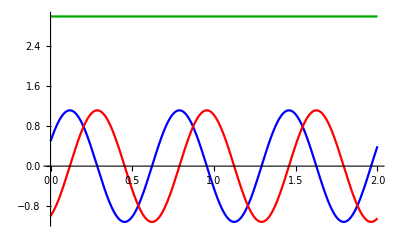

```mathematica
output[t_]:= (S2/.sol[[1]])[t];
Plot[{output[t][[1]],output[t][[2]],output[t][[3]]}, {t,0,2},PlotStyle->{Blue,Red,Darker[Green]}]
```

#### Vector definitions with numerical solution

```mathematica
S1v[t_]:=(S1/.sol[[1]])[t];
S2v[t_]:=(S2/.sol[[1]])[t];
Jv[t_]:=(J/.sol[[1]])[t];
Lv[t_]:=Jv[t]-S1v[t]-S2v[t];
Sv[t_]:=S1v[t]+S2v[t];
```

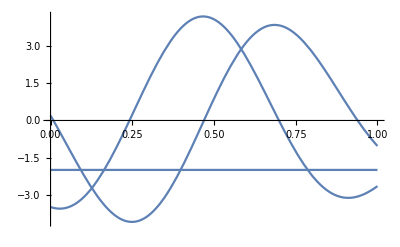

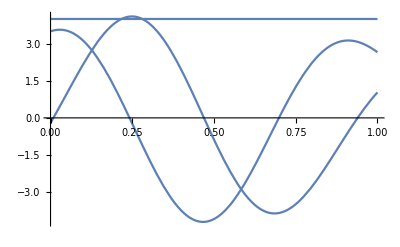

```mathematica
Plot[Lv[t],{t,0,1}]
Plot[Sv[t],{t,0,1}]
```

#### Vector modulus

```mathematica
NormS1[t_]:=Norm[S1v[t]];
NormS2[t_]:=Norm[S2v[t]];
NormJ[t_]:=Norm[Jv[t]];
NormL[t_]:=Norm[Lv[t]];
NormS[t_]:=Norm[Sv[t]];
```

#### Unit vector definitions

```mathematica
S1u[t_]:=S1v[t]/NormS1[t];
Su[t_]:=Sv[t]/NormS[t];
```

#### Cartesian unit vectors

```mathematica
zcap[t_]:={0,0,1}
```

```mathematica
xcap[t_]:={1,0,0}
```

```mathematica
ycap[t_]:=Cross[zcap[t],xcap[t]]
```

#### Orthogonal vector definition

```mathematica
SO1[t_]:=Cross[ycap[t],Sv[t]];
NormSO[t_]:=Norm[SO1[t]];
SOu[t_]:=SO1[t]/NormSO[t]
```

#### Angle ϕ' definitions

```mathematica
cosϕ1[t_]:=Dot[S1u[t],SOu[t]]/Norm[Cross[S1u[t],Su[t]]];
```

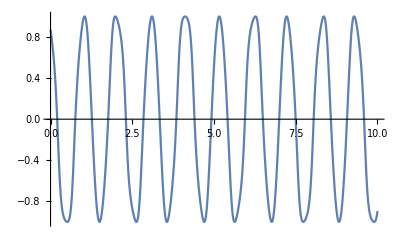

```mathematica
Plot[cosϕ1[t],{t,0,10},PlotRange->All]
```